```mathematica
vr[r_,θ_]:=  R[r] Cos[θ];
uθ[r_,θ_]:= Θ[r] Sin[θ];
uz[r_,θ_]:=0.0;
pL[r_,θ_]:=μ P[r] Cos[θ];
```

Boundary condition are all identically satisfied if the part of conditions is independent of θ:

```mathematica
R[b] = U; Θ[b] = -U;
```

The part of the boundary conditions independent of y are then satisfied if:

```mathematica
R[a]=0;aΘ'[a] = Θ[a] + R[a];
```

Solutions are:

```mathematica
R[r_] := (2 Log[r/a] (a^4+b^4)-b^2(r^2-a^4/r^2))/(2Log[b/a](a^4+b^4)-(b^4-a^4))U;
Θ[r_]:=- (2 Log[r/a] (a^4+b^4)+2(a^4+b^4)-b^2(3 r^2+a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
P[r_]:= -4(2 r b^2 +(a^4+b^4)/r)/(2 Log[b/a](a^4+b^4)-(b^4-a^4))U;
```

Likewise a z-dependent portion to the solution of the form:

```mathematica
vr[z_,r_]:= Cos[(n π z)/h] Rn[r];
uz[z_,r_]:= Sin[n π z/h]Zn[r];
pl[z_,r_]:= Subscript[μ, E] Cos[(n π z)/h]Pn[r];
```

```mathematica
Pn[rn_]:=(2 n π)/h(A BesselK[0,rn] + B BesselI[0,rn]);
Rn[rn_]:= A rn BesselK[0,rn] + B rn BesselI[0,rn]+𝒞 BesselK[1,rn] + 𝒟 BesselI[1,rn];
Zn[rn_]:= A *(rn BesselK[1,rn]-2 BesselK[0,rn])-B*(rn BesselI[1,rn]+2 BesselI[0,rn])+𝒞 BesselK[0,rn]-𝒟*BesselI[0,rn];
```

Simple special case where the weld pool is so large that S/L boundary can be considered arbitrarily far away:

```mathematica
A=(-w0 γ h^2)/(π^2 a^2 μ)* 1/(n^2 BesselK[1,n π a/h]);
𝒞=(w0 γ h)/(π a μ)*BesselK[0,n π a/h]/(n(BesselK[1,n π a/h])^2);
B=0; 𝒟=0;
```

```mathematica
w0=1; γ=0.1; a0=1; h=10; b0=10;μ=0.2; n=10;
```

```mathematica
A
```

-1.49382

```mathematica
𝒟
```

0

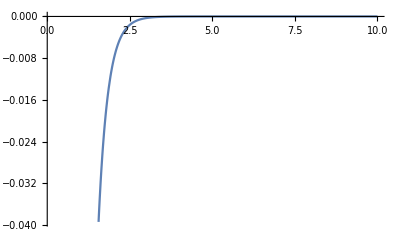

```mathematica
Plot[Pn[n π r/h],{r,0.1,10}]
```

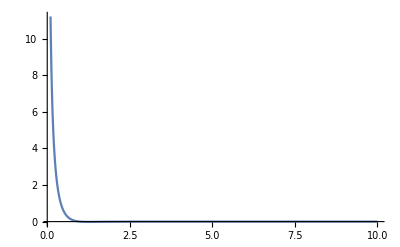

```mathematica
Plot[Rn[n π r/h],{r,0.1,10},PlotRange->All]
```

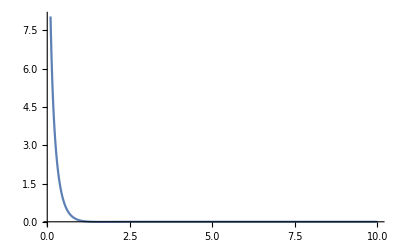

```mathematica
Plot[Zn[n π r/h],{r,0.1,10},PlotRange->All]
```

The final solutions are given as combinations of the results:

```mathematica
Button["Go to cell",NotebookLocate["Solutions"]]
```

Go to cell

```mathematica
ur[r0_,z_,θ_]:=Module[{rn = n π r0/h, an= n π a/h, zn=n π z/h, Up = τ h/(U π μ),a=a0/h,b=b0/h,r=r0/h},
(2 Log[r/a](a^4+b^4)-b^2(r^2-a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))Cos[θ]-
Up ∑_(n=1)^100 ((rn BesselK[0,rn])/(an BesselK[1,an])-(BesselK[0,an] BesselK[1,rn])/BesselK[1,an]^2) Cos[zn]/n];
uθ[r0_,θ_]:=Module[{a=a0/h,b=b0/h,r=r0/h}, (2(Log[r/a]+1)(a^4+b^4)-b^2(3 r^2+a^4/r^2))/(2 Log[b/a](a^4+b^4)-(b^4-a^4))Sin[θ]];
uz[r_,z_,θ_]:= Module[{rn=n π r/h, an = n π a/h, zn = n π z/h, Up=τ h/(U π μ)},
-Up ∑_(n=1)^100 (rn/an BesselK[1,rn]/BesselK[1,an]-BesselK[0,rn]*((an*BesselK[0,an]+2 BesselK[1,an])/(an BesselK[1,an]^2)))Sin[zn]/n];
```

```mathematica
U=1;τ=.2;
```

```mathematica
uz[0.1,0.1,1.2]
```

257.952

```mathematica
uθ[0.1,1.2]
```

-0.932039

```mathematica
ur[0.1,0.1,1.2]
```

1106.3

```mathematica
Convert[r_,θ_, z_,t_]:= {(ur[r,z,θ] Cos[θ]-uθ[r,θ] Sin[θ])t, (ur[r,z,θ] Sin[θ]+uθ[r,θ] Cos[θ])*t, uz[r,z,θ]*t};
```

```mathematica
Convert[0.1,0.1,1.2,0.001]
```

{-0.937661,-0.0941802,-0.490654}

```mathematica
StreamPlot3D[Convert[Sqrt[x^2+y^2],ArcTan[y/x],z,1.],{x,-b0,b0},{y,-10,10},{z,0.1,10},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
StreamPlot3D[Convert[Sqrt[x^2+y^2],0,z],{x,-b0,b0},{y,-10,10},{z,0.1,10},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Δt=0.1;
```

```mathematica
start = {0.1,0.1,5.0};
times = Table[Δt * i, {i,100}];
```

```mathematica
points=Map[Convert[start[[1]],start[[2]],start[[3]],#]&,times]
```

{{-93.7661,-9.41802,-49.0654},{-187.532,-18.836,-98.1308},{-281.298,-28.2541,-147.196},{-375.064,-37.6721,-196.262},{-468.83,-47.0901,-245.327},{-562.596,-56.5081,-294.392},{-656.362,-65.9261,-343.458},{-750.128,-75.3442,-392.523},{-843.894,-84.7622,-441.589},{-937.661,-94.1802,-490.654},{-1031.43,-103.598,-539.719},{-1125.19,-113.016,-588.785},{-1218.96,-122.434,-637.85},{-1312.72,-131.852,-686.915},{-1406.49,-141.27,-735.981},{-1500.26,-150.688,-785.046},{-1594.02,-160.106,-834.112},{-1687.79,-169.524,-883.177},{-1781.56,-178.942,-932.242},{-1875.32,-188.36,-981.308},{-1969.09,-197.778,-1030.37},{-2062.85,-207.196,-1079.44},{-2156.62,-216.614,-1128.5},{-2250.39,-226.032,-1177.57},{-2344.15,-235.45,-1226.63},{-2437.92,-244.869,-1275.7},{-2531.68,-254.287,-1324.77},{-2625.45,-263.705,-1373.83},{-2719.22,-273.123,-1422.9},{-2812.98,-282.541,-1471.96},{-2906.75,-291.959,-1521.03},{-3000.51,-301.377,-1570.09},{-3094.28,-310.795,-1619.16},{-3188.05,-320.213,-1668.22},{-3281.81,-329.631,-1717.29},{-3375.58,-339.049,-1766.35},{-3469.34,-348.467,-1815.42},{-3563.11,-357.885,-1864.48},{-3656.88,-367.303,-1913.55},{-3750.64,-376.721,-1962.62},{-3844.41,-386.139,-2011.68},{-3938.17,-395.557,-2060.75},{-4031.94,-404.975,-2109.81},{-4125.71,-414.393,-2158.88},{-4219.47,-423.811,-2207.94},{-4313.24,-433.229,-2257.01},{-4407.,-442.647,-2306.07},{-4500.77,-452.065,-2355.14},{-4594.54,-461.483,-2404.2},{-4688.3,-470.901,-2453.27},{-4782.07,-480.319,-2502.33},{-4875.83,-489.737,-2551.4},{-4969.6,-499.155,-2600.47},{-5063.37,-508.573,-2649.53},{-5157.13,-517.991,-2698.6},{-5250.9,-527.409,-2747.66},{-5344.67,-536.827,-2796.73},{-5438.43,-546.245,-2845.79},{-5532.2,-555.663,-2894.86},{-5625.96,-565.081,-2943.92},{-5719.73,-574.499,-2992.99},{-5813.5,-583.917,-3042.05},{-5907.26,-593.335,-3091.12},{-6001.03,-602.753,-3140.18},{-6094.79,-612.171,-3189.25},{-6188.56,-621.589,-3238.32},{-6282.33,-631.007,-3287.38},{-6376.09,-640.425,-3336.45},{-6469.86,-649.843,-3385.51},{-6563.62,-659.261,-3434.58},{-6657.39,-668.679,-3483.64},{-6751.16,-678.097,-3532.71},{-6844.92,-687.515,-3581.77},{-6938.69,-696.933,-3630.84},{-7032.45,-706.351,-3679.9},{-7126.22,-715.77,-3728.97},{-7219.99,-725.188,-3778.04},{-7313.75,-734.606,-3827.1},{-7407.52,-744.024,-3876.17},{-7501.28,-753.442,-3925.23},{-7595.05,-762.86,-3974.3},{-7688.82,-772.278,-4023.36},{-7782.58,-781.696,-4072.43},{-7876.35,-791.114,-4121.49},{-7970.11,-800.532,-4170.56},{-8063.88,-809.95,-4219.62},{-8157.65,-819.368,-4268.69},{-8251.41,-828.786,-4317.75},{-8345.18,-838.204,-4366.82},{-8438.94,-847.622,-4415.89},{-8532.71,-857.04,-4464.95},{-8626.48,-866.458,-4514.02},{-8720.24,-875.876,-4563.08},{-8814.01,-885.294,-4612.15},{-8907.78,-894.712,-4661.21},{-9001.54,-904.13,-4710.28},{-9095.31,-913.548,-4759.34},{-9189.07,-922.966,-4808.41},{-9282.84,-932.384,-4857.47},{-9376.61,-941.802,-4906.54}}

```mathematica
points=NestList[Convert[#[[1]],#[[2]],#[[3]],0.0001]&,start,100];
```

```mathematica
ListPointPlot3D[Re[points],PlotRange->All]
```

-Graphics3D-

```mathematica
Re[points]
```

{{0.1,0.1,5.},{-0.115878,-0.0116366,5.11137×10^-17},{-0.0968611,0.00112817,1.18939×10^-17},{-0.113694,-0.000172836,2.8233×10^-17},{-0.0850179,0.0000193032,2.95617×10^-18},{-0.0802698,-3.14359×10^-6,9.76352×10^-18},{-0.0742886,3.58229×10^-7,7.86762×10^-19},{-0.0727794,-5.85133×10^-8,2.71186×10^-18},{-0.0713455,6.68756×10^-9,2.09068×10^-19},{-0.0709394,-1.09298×10^-9,7.21235×10^-19},{-0.070568,1.25001×10^-10,5.50286×10^-20},{-0.0704598,-2.04324×10^-11,1.8977×10^-19},{-0.0703617,2.33718×10^-12,1.44404×10^-20},{-0.0703328,-3.82046×10^-13,4.97925×10^-20},{-0.0703068,4.37025×10^-14,3.78625×10^-21},{-0.0702991,-7.14389×10^-15,1.3055×10^-20},{-0.0702922,8.17204×10^-16,9.92525×10^-22},{-0.0702901,-1.33586×10^-16,3.4222×10^-21},{-0.0702883,1.52812×10^-17,2.60164×10^-22},{-0.0702877,-2.49797×10^-18,8.97036×10^-22},{-0.0702872,2.85749×10^-19,6.8194×10^-23},{-0.0702871,-4.67105×10^-20,2.3513×10^-22},{-0.070287,5.34333×10^-21,1.78749×10^-23},{-0.0702869,-8.73458×10^-22,6.16319×10^-23},{-0.0702869,9.99171×10^-23,4.68533×10^-24},{-0.0702869,-1.63331×10^-23,1.61548×10^-23},{-0.0702869,1.86839×10^-24,1.22811×10^-24},{-0.0702869,-3.0542×10^-25,4.23447×10^-24},{-0.0702869,3.49378×10^-26,3.2191×10^-25},{-0.0702869,-5.71117×10^-27,1.10993×10^-24},{-0.0702869,6.53315×10^-28,8.43782×10^-26},{-0.0702869,-1.06795×10^-28,2.90933×10^-25},{-0.0702869,1.22166×10^-29,2.2117×10^-26},{-0.0702869,-1.99701×10^-30,7.62587×10^-26},{-0.0702869,2.28443×10^-31,5.79727×10^-27},{-0.0702869,-3.73429×10^-32,1.99888×10^-26},{-0.0702869,4.27175×10^-33,1.51957×10^-27},{-0.0702869,-6.9829×10^-34,5.23941×10^-27},{-0.0702869,7.98791×10^-35,3.98306×10^-28},{-0.0702869,-1.30576×10^-35,1.37334×10^-27},{-0.0702869,1.49369×10^-36,1.04403×10^-28},{-0.0702869,-2.44169×10^-37,3.59978×10^-28},{-0.0702869,2.79311×10^-38,2.73659×10^-29},{-0.0702869,-4.56582×10^-39,9.43566×10^-29},{-0.0702869,5.22296×10^-40,7.1731×10^-30},{-0.0702869,-8.53781×10^-41,2.47325×10^-29},{-0.0702869,9.76661×10^-42,1.8802×10^-30},{-0.0702869,-1.59652×10^-42,6.48284×10^-30},{-0.0702869,1.8263×10^-43,4.92833×10^-31},{-0.0702869,-2.98539×10^-44,1.69927×10^-30},{-0.0702869,3.41507×10^-45,1.2918×10^-31},{-0.0702869,-5.58251×10^-46,4.45409×10^-31},{-0.0702869,6.38597×10^-47,3.38605×10^-32},{-0.0702869,-1.0439×10^-47,1.1675×10^-31},{-0.0702869,1.19414×10^-48,8.87544×10^-33},{-0.0702869,-1.95202×10^-49,3.06022×10^-32},{-0.0702869,2.23297×10^-50,2.32641×10^-33},{-0.0702869,-3.65016×10^-51,8.02137×10^-33},{-0.0702869,4.17551×10^-52,6.09794×10^-34},{-0.0702869,-6.82559×10^-53,2.10254×10^-33},{-0.0702869,7.80796×10^-54,1.59838×10^-34},{-0.0702869,-1.27634×10^-54,5.51114×10^-34},{-0.0702869,1.46004×10^-55,4.18964×10^-35},{-0.0702869,-2.38669×10^-56,1.44457×10^-34},{-0.0702869,2.73019×10^-57,1.09818×10^-35},{-0.0702869,-4.46296×10^-58,3.78647×10^-35},{-0.0702869,5.10529×10^-59,2.87852×10^-36},{-0.0702869,-8.34546×10^-60,9.92503×10^-36},{-0.0702869,9.54659×10^-61,7.54512×10^-37},{-0.0702869,-1.56055×10^-61,2.60153×10^-36},{-0.0702869,1.78515×10^-62,1.97771×10^-37},{-0.0702869,-2.91814×10^-63,6.81907×10^-37},{-0.0702869,3.33813×10^-64,5.18393×10^-38},{-0.0702869,-5.45674×10^-65,1.7874×10^-37},{-0.0702869,6.2421×10^-66,1.3588×10^-38},{-0.0702869,-1.02038×10^-66,4.68509×10^-38},{-0.0702869,1.16724×10^-67,3.56166×10^-39},{-0.0702869,-1.90805×10^-68,1.22805×10^-38},{-0.0702869,2.18266×10^-69,9.33575×10^-40},{-0.0702869,-3.56793×10^-70,3.21893×10^-39},{-0.0702869,4.08145×10^-71,2.44707×10^-40},{-0.0702869,-6.67182×10^-72,8.43739×10^-40},{-0.0702869,7.63206×10^-73,6.4142×10^-41},{-0.0702869,-1.24759×10^-73,2.21159×10^-40},{-0.0702869,1.42715×10^-74,1.68128×10^-41},{-0.0702869,-2.33292×10^-75,5.79697×10^-41},{-0.0702869,2.66868×10^-76,4.40693×10^-42},{-0.0702869,-4.36242×10^-77,1.51949×10^-41},{-0.0702869,4.99028×10^-78,1.15513×10^-42},{-0.0702869,-8.15746×10^-79,3.98286×10^-42},{-0.0702869,9.33152×10^-80,3.02781×10^-43},{-0.0702869,-1.5254×10^-80,1.04398×10^-42},{-0.0702869,1.74494×10^-81,7.93644×10^-44},{-0.0702869,-2.8524×10^-82,2.73645×10^-43},{-0.0702869,3.26293×10^-83,2.08028×10^-44},{-0.0702869,-5.33381×10^-84,7.17273×10^-44},{-0.0702869,6.10148×10^-85,5.45279×10^-45},{-0.0702869,-9.97391×10^-86,1.8801×10^-44},{-0.0702869,1.14094×10^-86,1.42927×10^-45},{-0.0702869,-1.86506×10^-87,4.92808×10^-45},{-0.0702869,2.13349×10^-88,3.74638×10^-46}}